```mathematica
α = 0.0072973525693;
Subscript[m, e]=510998.95;(*eV*)
Subscript[m, p] = 938.27208816×10^6;(*eV*)
Subscript[ϵ, 0]=13.6 ;(*eV*)
Subscript[T, 0]=2.34865477×10^-4;(*eV*)
Subscript[m, pl]=1.2211×10^28 ;(*eV*)
Subscript[Ω, m]=0.315;
Subscript[Ω, b]=0.04924319136;
Subscript[ρ, c] = 3.679272179×10^-11;(*eV^4*)
effdof = 2+6×7/8×(4/11)^(4/3); (*effective degrees of freedom, only including photons and neutrinos*)
Subscript[m, H] = Subscript[m, e]+Subscript[m, p]+Subscript[ϵ, 0]; (*eV*)
Subscript[m, He] = 3728401306; (*eV*)
Subscript[z, reio] = 7.7;
Subscript[Y, p] = 0.245;
Subscript[f, He] = Subscript[m, H]/Subscript[m, He]×Subscript[Y, p]/(1-Subscript[Y, p]);
```

```mathematica
(*baryon density*)
nb[z_] := Subscript[Ω, b]×Subscript[ρ, c]/Subscript[m, p]×(1+z)^3
(*alpha*)
recrate[z_] := 9.78×(α^2/Subscript[m, e]^2)×Sqrt[Subscript[ϵ, 0]/(Subscript[T, 0]×(1+z))]×Log[Subscript[ϵ, 0]/(Subscript[T, 0]×(1+z))]
(*beta*)
ionrate[z_] := 9.78×(α^2/Subscript[m, e]^2)×Sqrt[Subscript[ϵ, 0]/(Subscript[T, 0]×(1+z))]×Log[Subscript[ϵ, 0]/(Subscript[T, 0]×(1+z))]×((Subscript[m, e]×Subscript[T, 0]×(1+z))/(2×Pi))^(3/2)×Exp[-Subscript[ϵ, 0]/(Subscript[T, 0]×(1+z))]
(*hubble*)
hubble[z_] := Sqrt[(8×Pi)/(3×Subscript[m, pl]^2)×(Subscript[Ω, m] ×Subscript[ρ, c] ×(1+z)^3+effdof×Pi^2/30×(Subscript[T, 0]×(1+z))^4)] 
(*reionisation part*)
y[z_] := (1+z)^(3/2)
Subscript[y, reio] = y[z]/.{z->Subscript[z, reio]};
Deltay[z_] := 3/2×Sqrt[1+z]×0.015×(1+z)
Xreio[z_] := (1+Subscript[f, He])/2×(1+Tanh[(Subscript[y, reio]-y[z])/Deltay[z]])
```

```mathematica
Xdiff[z_] := -((1-xe[z])×ionrate[z] - (xe[z])^2×nb[z]×recrate[z])/((1+z)×hubble[z])
```

```mathematica
Subscript[z, i] = 0;
Subscript[z, f] = 1900;
sol = NDSolve[{xe'[z] == Xdiff[z], xe[Subscript[z, f]]==1},xe[z], {z,Subscript[z, i],Subscript[z, f]}]
```

{{xe[z]→InterpolatingFunction[…][z]}}

```mathematica
Subscript[X, e][z_] := xe[z]/.sol[[1]]
Subscript[X, etot][z_] := Subscript[X, e][z]+Xreio[z]
```

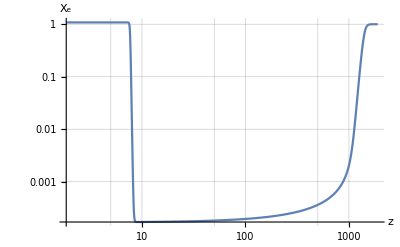

```mathematica
LogLogPlot[Subscript[X, etot][z], {z,Subscript[z, i],Subscript[z, f]},AxesLabel->{"z","X_e"},GridLines->Automatic,PlotRange->All]
```

```mathematica
Subscript[X, etot][z]/.{z->Subscript[z, i]}
```

1.08188